# Dynamical Analysis of a Referential Communication Task

## Thomas Gaul

## Initialization

```mathematica
Get["Dynamica`"];
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
(* if CTRNN5y takes too long to define, edit Dynamica.m and lower the
$DynamicaSymbolicThreshold (the default is 5). Use this line to verify. *)
$DynamicaSymbolicThreshold
```

4

### Definitions for Loading Phenotype

```mathematica
$ParentDirectory = FileNameJoin[{NotebookDirectory[],"..","EvoP2"}];
SetDirectory[$ParentDirectory];
fileName[pop_]:=FileNameJoin[{StringJoin["Pop-",ToString[pop]],"phenotype.dat"}];
SetPhenotype[pop_]:=Module[{data,taus,thetas,weights,sensorweights},data=Flatten[Import[fileName[pop],"Table"]];
taus=data[[1;;5]];
thetas=data[[6;;10]];
weights=Partition[data[[11;;35]],5];
sensorweights=data[[36;;]];
CTRNN5y/.{
τ1->taus[[1]],τ2->taus[[2]],τ3->taus[[3]],τ4->taus[[4]],τ5->taus[[5]],
θ1->thetas[[1]],θ2->thetas[[2]],θ3->thetas[[3]],θ4->thetas[[4]],θ5->thetas[[5]],
w11->weights[[1,1]],w21->weights[[2,1]],w31->weights[[3,1]],w41->weights[[4,1]],w51->weights[[5,1]],
w12->weights[[1,2]],w22->weights[[2,2]],w32->weights[[3,2]],w42->weights[[4,2]],w52->weights[[5,2]],
w13->weights[[1,3]],w23->weights[[2,3]],w33->weights[[3,3]],w43->weights[[4,3]],w53->weights[[5,3]],
w14->weights[[1,4]],w24->weights[[2,4]],w34->weights[[3,4]],w44->weights[[4,4]],w54->weights[[5,4]],
w15->weights[[1,5]],w25->weights[[2,5]],w35->weights[[3,5]],w45->weights[[4,5]],w55->weights[[5,5]],
sw1->sensorweights[[1]],sw2->sensorweights[[2]],sw3->sensorweights[[3]],sw4->sensorweights[[4]],sw5->sensorweights[[5]]
}
];
```

```mathematica
ParametersReduced={sw1->15.984208000000000637896846455988`31.203691122324884,sw2->-4.9543999999999996930455381516367`31.694991067001517,w11->9.3822720000000003892637323588133`31.97230801935797,w12->-6.7681120000000003500417733448558`31.830467536877823,w21->9.4172320000000002693241185625084`31.973923269695344,w22->9.2989440000000005426272764452733`31.96843363231605,
w41->1.7425440000000000928537247091299`31.241183753034584,w42->-13.6319999999999996731503415503539999999999999999999999999999`31.134559577422625,
θ1->-14.3195519999999998361772668431510000000000000000000000000001`31.15592943089283,θ2->15.1902559999999997586428435170089999999999999999999999999999`31.181565093049784,
τ1->29.980830999999998454086380661465`31.4768436663279,τ2->16.657316049999998597286321455613`31.22160502596773};
```

### Dynamical System Definitions

```mathematica
σ[x_]:=1/(1+ⅇ^-x);
```

#### 5-Dimensional System in State Space

```mathematica
CTRNN5y=DynamicalSystem[
{
(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+w31 σ[y3+θ3]+w41 σ[y4+θ4]+w51 σ[y5+θ5]+sw1 d)/τ1,
(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2]+w32 σ[y3+θ3]+w42 σ[y4+θ4]+w52 σ[y5+θ5]+sw2 d)/τ2,
(-y3+w13 σ[y1+θ1]+w23 σ[y2+θ2]+w33 σ[y3+θ3]+w43 σ[y4+θ4]+w53 σ[y5+θ5]+sw3 d)/τ3,
(-y4+w14 σ[y1+θ1]+w24 σ[y2+θ2]+w34 σ[y3+θ3]+w44 σ[y4+θ4]+w54 σ[y5+θ5]+sw4 d)/τ4,
(-y5+w15 σ[y1+θ1]+w25 σ[y2+θ2]+w35 σ[y3+θ3]+w45 σ[y4+θ4]+w55 σ[y5+θ5]+sw5 d)/τ5
},
{{y1,-35,35},{y2,-35,35},{y3,-35,35},{y4,-35,35},{y5,-35,35}},
{
{θ1,-16,16},{θ2,-16,16},{θ3,-16,16},{θ4,-16,16},{θ5,-16,16},
{τ1,1,30},{τ2,1,30},{τ3,1,30},{τ4,1,30},{τ5,1,30},
{sw1,-16,16},{sw2,-16,16},{sw3,-16,16},{sw4,-16,16},{sw5,-16,16},
{w11,-16,16},{w21,-16,16},{w31,-16,16},{w41,-16,16},{w51,-16,16},
{w12,-16,16},{w22,-16,16},{w32,-16,16},{w42,-16,16},{w52,-16,16},
{w13,-16,16},{w23,-16,16},{w33,-16,16},{w43,-16,16},{w53,-16,16},
{w14,-16,16},{w24,-16,16},{w34,-16,16},{w44,-16,16},{w54,-16,16},
{w15,-16,16},{w25,-16,16},{w35,-16,16},{w45,-16,16},{w55,-16,16},
{d,0,1}
}
];
```

#### 2-Dimensional Reduction in State Space

```mathematica
A2d=DynamicalSystem[
{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+w41 +sw1 d)/τ1,
(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2]+w42 +sw2 d)/τ2},
{{y1,-35,35},{y2,-35,35}},
{
{w11,-16,16},{w21,-16,16},{w12,-16,16},{w22,-16,16},
{w41,-16,16},{w42,-16,16},
{sw1,-16,16},{sw2,-16,16},
{τ1,1,30},{τ2,1,30},
{θ1,-16,16},{θ2,-16,16},
{d,0,1}
}
];
```

### Loading Agent Phenotype

```mathematica
(* using agent 1 for dynamical analysis *)
A = SetPhenotype[1];
A2d=A2d/.ParametersReduced;
```

### Transformation of Reduced Form to Output Space

```mathematica
With[{ε=10^-5},
Ao2d=TransformDynamicalSystem[A2d,{{o1,ε,1-ε},{o2,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2]}]
];
```

## Phase Plane Analysis

### Time Scale in 5D System

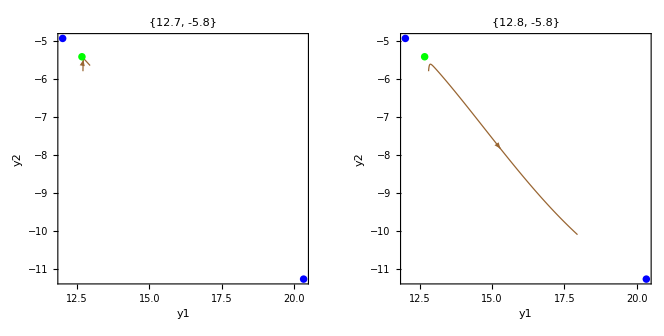

```mathematica
GraphicsRow[{
Show[
DisplayPhasePortrait[A/.{d->0},StateVariables->{y1,y2},Tries->100,PlotRange->All,EquilibriumPointStyle->{PointSize[0.03]}],
DisplayTrajectories[A/.{d->0},{{12.7,-5.8,-1.0222608056533848,29.599883008269867,-2.789352727820398}},200,StateVariables->{y1,y2},PlotRange->All,PlotPoints->250,PlotStyle->{Thickness[.005],Brown}],
ImageSize->Small,PlotLabel->"{12.7, -5.8}"
],
Show[
DisplayPhasePortrait[A/.{d->0},StateVariables->{y1,y2},Tries->100,PlotRange->All,EquilibriumPointStyle->{PointSize[0.03]}],
DisplayTrajectories[A/.{d->0},{{12.8,-5.8,-1.0222608056533848,29.599883008269867,-2.789352727820398}},200,StateVariables->{y1,y2},PlotRange->All,PlotPoints->250,PlotStyle->{Thickness[.005],Brown}],
ImageSize->Small,PlotLabel->"{12.8, -5.8}"
]
}]
```

```mathematica
Print["y1 Time Constant: ",A[[9,-5]]]
Print["y2 Time Constant: ",A[[9,-4]]]
Print["y3 Time Constant: ",A[[9,-3]]]
Print["y4 Time Constant: ",A[[9,-2]]]
Print["y5 Time Constant: ",A[[9,-1]]]
```

y1 Time Constant: τ1→29.98083099999999845408638066147

y2 Time Constant: τ2→16.65731604999999859728632145561

y3 Time Constant: τ3→2.053627999999999786950866109692

y4 Time Constant: τ4→29.96783899999999789542926009744

y5 Time Constant: τ5→6.260788500000000311729309032671

```mathematica
eps=EquilibriumPoints[A/.{d->0}]
SaddlePoint=eps[[2,3]]
```

{EquilibriumPoint[Stable,Node,{11.9971,-4.93765,-1.02226,29.5999,-2.78935}],EquilibriumPoint[Saddle,Node,{12.6648,-5.41964,-2.00339,29.0862,-2.60136}],EquilibriumPoint[Stable,Node,{20.3372,-11.2645,-13.5685,22.7658,-0.442715}]}

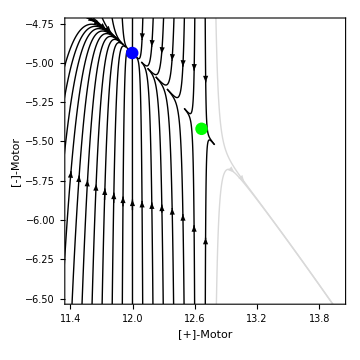

```mathematica
flow=Flatten[Table[Join[{12+i,-4.9-j},SaddlePoint[[3;;]]],{i,-1,.7,.1},{j,-.2,2,2.1}],1];
window={{11.4,14},{-6.5,-4.75}};
fig12=Show[
DisplayTrajectories[A/.{d->0},flow,130,StateVariables->{y1,y2},PlotRange->window,Arrows->1,PlotStyle->Black,FrameLabel->{"[+]-Motor","[-]-Motor"}],
DisplayTrajectories[A/.{d->0},{Join[{12.8,-4.6},SaddlePoint[[3;;]]],Join[{12.8,-6.9},SaddlePoint[[3;;]]]},150,StateVariables->{y1,y2},PlotRange->window,Arrows->1,PlotStyle->LightGray],
DisplayPhasePortrait[A/.{d->0},StateVariables->{y1,y2},Tries->100,PlotRange->window],
ImageSize->Medium
]
```

### Analysis of Reduced Form in State Space

#### Phase Portrait

```mathematica
EquilibriumPoints[A/.{d->0}]
EquilibriumPoints[A2d/.{d->0}]
```

{EquilibriumPoint[Stable,Node,{11.9971,-4.93765,-1.02226,29.5999,-2.78935}],EquilibriumPoint[Saddle,Node,{12.6648,-5.41964,-2.00339,29.0862,-2.60136}],EquilibriumPoint[Stable,Node,{20.3372,-11.2645,-13.5685,22.7658,-0.442715}]}

{EquilibriumPoint[Stable,Node,{11.9971,-4.93764}],EquilibriumPoint[Saddle,Node,{12.6648,-5.41968}],EquilibriumPoint[Stable,Node,{20.337,-11.2646}]}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 215.915 and t = 218.51.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 301.859 and t = 305.297.

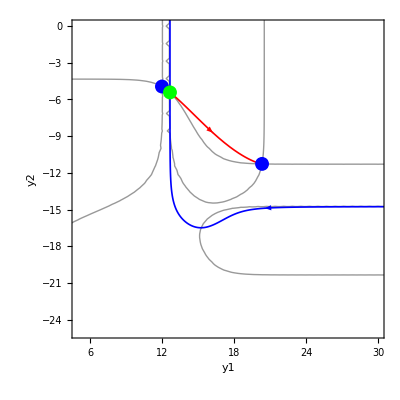

```mathematica
DisplayPhasePortrait[A2d/.{d->0},Tries->300,NullManifolds->True,PlotRange->{{5,30},{-25,0}},SaddleManifolds->True,SaddleManifoldPlotPoints->1000,SaddleManifoldDuration->5000]
```

#### Time-scale

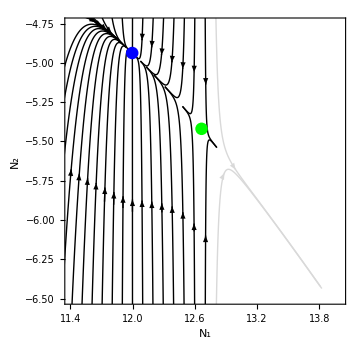

```mathematica
flow=Flatten[Table[{12+i,-4.9-j},{i,-1,.7,.1},{j,-.2,2,2.1}],1];
window={{11.4,14},{-6.5,-4.75}};
Show[
DisplayTrajectories[A2d/.{d->0},flow,145,StateVariables->{y1,y2},PlotRange->window,Arrows->1,PlotStyle->Black,FrameLabel->{"N_1","N_2"},LabelStyle->Directive[ Medium,Gray,FontFamily->"Ariel"]],
DisplayTrajectories[A2d/.{d->0},{{12.8,-4.6},{12.8,-6.9}},145,StateVariables->{y1,y2},PlotRange->window,Arrows->1,PlotStyle->LightGray],
DisplayPhasePortrait[A2d/.{d->0},StateVariables->{y1,y2},Tries->100,PlotRange->window],
ImageSize->Medium
]
```

### Analysis of Reduced Form in Output-Space

#### Phase Portrait

```mathematica
eps=EquilibriumPoints[Ao2d/.{d->0}]
```

{EquilibriumPoint[Stable,Node,{0.0892797,0.999965}],EquilibriumPoint[Saddle,Node,{0.160473,0.999943}],EquilibriumPoint[Stable,Node,{0.99757,0.980652}]}

DisplayPhasePortrait::optx: Unknown option {LabelStyle} in {Tries→300,SaddleManifolds→True,SaddleManifoldDuration→1000,«24»→1000,«13»→False,PlotRange→{{-0.05,1.05},{-0.05,1.05}},FrameLabel→{N_1,N_2},LabelStyle→Directive[Medium,color,FontFamily→Ariel]}.

LessEqual::nord: Invalid comparison with 1.-1.2974×10^-10 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

NDSolve::nbnum1: The function value !9.×10^-6≤1.-1.2974×10^-10 ⅈ≤1.09999 is not True or False when the arguments are {146.999,1.-1.2974×10^-10 ⅈ,0.605944+0. ⅈ}.

NDSolve::nbnum1: The function value !(9.×10^-6≤1.-5.11191×10^-10 ⅈ≤1.09999&&9.×10^-6≤0.606147+1.53361×10^-11 ⅈ≤1.09999) is not True or False when the arguments are {149.844,1.-5.11191×10^-10 ⅈ,0.606147+1.53361×10^-11 ⅈ}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 25000 steps reached at the point t == 193.475.

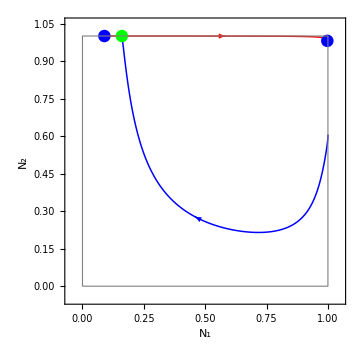

```mathematica
Show[
DisplayPhasePortrait[Ao2d/.{d->0},Tries->300,SaddleManifolds->True,SaddleManifoldDuration->1000,SaddleManifoldPlotPoints->1000,NullManifolds->False,
PlotRange->{{-.05,1.05},{-.05,1.05}},FrameLabel->{"N_1","N_2"},LabelStyle->Directive[ Medium,Gray,FontFamily->"Ariel"]]
,Graphics[{EdgeForm[{Thin,Gray,Dashed}],FaceForm[],Rectangle[{0,0},{1,1}]}]
(*,Graphics[Text[Framed[Style["P = 1",Black,Italic,12,FontFamily->"Times"],
FrameMargins->1,Background->White,FrameStyle->LightGray],eps[[1,3]]+{-.01,-.05}]]
,Graphics[Text[Framed[Style["P = 2",Black,Italic,12,FontFamily->"Times"],
FrameMargins->1,Background->White,FrameStyle->LightGray],eps[[3,3]]+{-.02,-.05}]]*)
,ImageSize->Medium
]
```

#### Timescale in F-Motor Space

```mathematica
equ=EquilibriumPoints[Ao2d/.{d->0},Tries->300]
saddle=equ[[2,3]]
```

{EquilibriumPoint[Stable,Node,{0.0892797,0.999965}],EquilibriumPoint[Saddle,Node,{0.160473,0.999943}],EquilibriumPoint[Stable,Node,{0.99757,0.980652}]}

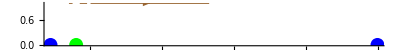

```mathematica
Show[
DisplayPhasePortrait[Ao2d/.{d->0},Tries->300,StateVariables->{o1},PlotRange->{0.05,.4}],
DisplayTrajectories[Ao2d/.{d->0},{saddle+{0.01,0},saddle-{0.01,0},saddle+{0.04,0}},100]
]
```

#### Step-Points

```mathematica
p1Phase1=Flatten[Import[FileNameJoin[{NotebookDirectory[],"p1_phase1.txt"}],"Table"]];
p1Phase2=Flatten[Import[FileNameJoin[{NotebookDirectory[],"p1_phase2.txt"}],"Table"]];
p2Phase3=Flatten[Import[FileNameJoin[{NotebookDirectory[],"p2_phase3.txt"}],"Table"]];
```

```mathematica
(* motor2 must be approximated due to saturation *)
SaddlePoint=EquilibriumPoints[A2d/.{d->0},Tries->300][[2,3]];
Attractor=EquilibriumPoints[A2d/.{d->0},Tries->300][[1,3]];
(* linear approximation to unstable saddle manifold *)
m=(Attractor[[2]]-SaddlePoint[[2]])/(Attractor[[1]]-SaddlePoint[[1]]);
b=SaddlePoint[[2]]-m*SaddlePoint[[1]];
Subscript[σ, -1][x_]:=Log[x/(1-x)]-θ1/.ParametersReduced;
StateFromOut[x_]:={Subscript[σ, -1][x],m Subscript[σ, -1][x]+b};
```

```mathematica
(* manually correcting points to land on transient/manifold *)
p1Phase2Traj=Thread[StateFromOut[p1Phase2]];
p1Phase2Traj = (p1Phase2Traj+{{0,0},{0,-.06},{0,.005},{0,.005}});
```

```mathematica
p1Phase2Traj
```

{{9.21886,-2.93204},{11.6136,-4.72076},{12.044,-4.96647},{12.593,-5.36282}}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 215.88 and t = 218.475.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 301.675 and t = 305.1.

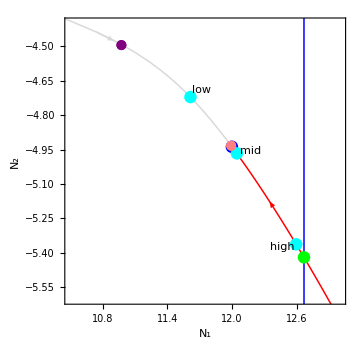

```mathematica
Show[
DisplayTrajectories[A2d/.{d->0},{{0,0}},1000,PlotStyle->{LightGray,Thickness[.003]},Arrows->10,PlotRange->{{10.5,13},{-5.6,-4.4}},FrameLabel->{"N_1","N_2"},LabelStyle->Directive[ Medium,Gray,FontFamily->"Ariel"]]
,DisplayPhasePortrait[A2d/.{d->0},Tries->300,SaddleManifolds->True,SaddleManifoldDuration->1500,SaddleManifoldPlotPoints->1000,SaddleManifoldArrows->1,MaxIterations->1000]
,ListPlot[p1Phase2Traj,PlotStyle->{Cyan,PointSize[0.025]}]
,ListPlot[{StateFromOut[p1Phase1[[1]]]-{0,.295}},PlotStyle->{Purple,PointSize[0.02]}]
,ListPlot[{StateFromOut[p2Phase3[[1]]]},PlotStyle->{Pink,PointSize[0.02]}]
,Graphics[Text[Framed[Style["low",Black,Italic,12,FontFamily->"Arial"],
Background->None,FrameStyle->None],p1Phase2Traj[[2]]+{.1,.03}]]
,Graphics[Text[Framed[Style["mid",Black,Italic,12,FontFamily->"Arial"],
Background->None,FrameStyle->None],p1Phase2Traj[[3]]+{.13,.01}]]
,Graphics[Text[Framed[Style["high",Black,Italic,12,FontFamily->"Arial"],
Background->None,FrameStyle->None],p1Phase2Traj[[4]]+{-.13,-.01}]]
,ImageSize->Medium
]
```

```mathematica
(* Minimum bounds for the distinguishable range *)
{p2Phase3[[1]],p1Phase2[[3]]}
```

{0.0887282,0.093164}

#### Verifying Saddle-to-Unstable Reduction

```mathematica
saddle2=EquilibriumPoints[A2d/.{d->.3},Tries->1000][[1,3]]
saddle5=EquilibriumPoints[A/.{d->.3},Tries->1000][[1,3]]
```

{14.5137,-16.0347}

{14.5137,-16.0347,-11.4858,19.8771,-4.40929}

```mathematica
sys5=A[[10]]/.A[[9]];
egv5=Eigenvalues[sys5/.Thread[A[[3]]->saddle5]];
egv5
```

{-0.486943+0. ⅈ,-0.159725+0. ⅈ,0.0507392+0.0812506 ⅈ,0.0507392-0.0812506 ⅈ,-0.0333688+0. ⅈ}

```mathematica
egv2=Eigenvalues[A2d[[10]]]/.ParametersReduced;
egv2/.Thread[A2d[[3]]->saddle2]
```

{0.0507393-0.0812506 ⅈ,0.0507393+0.0812506 ⅈ}

## Bifurcation Analysis

### Bifurcation Diagrams of Fixed Points

#### State-Space

```mathematica
DisplayBifurcationDiagram[A2d,d]
```

Warning: MaxSteps exceeded, terminating branch

Warning: MaxSteps exceeded, terminating branch

-Graphics3D-

#### Output-Space

```mathematica
DisplayBifurcationDiagram[Ao2d,d]
```

-Graphics3D-

### Full Bifurcation Diagram

#### Finding the limit cycle

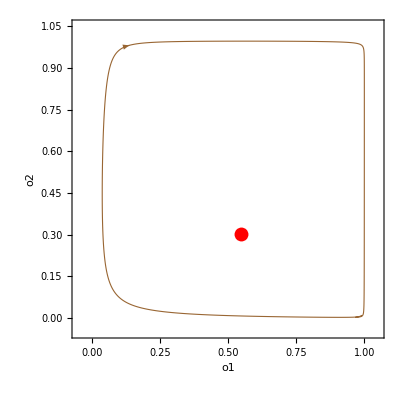

```mathematica
Show[
DisplayPhasePortrait[Ao2d/.{d->.3},PlotRange->{{-.05,1.05},{-.05,1.05}}],
DisplayTrajectories[Ao2d/.{d->.3},{{.99,.01}},270,PlotPoints->1000]
]
```

```mathematica
LC=FindLimitCycle[Ao2d/.{d->.3},Last[First[$Trajectories]],270]
```

LimitCycle[Stable,255.384,{0.967199,0.00265821}]

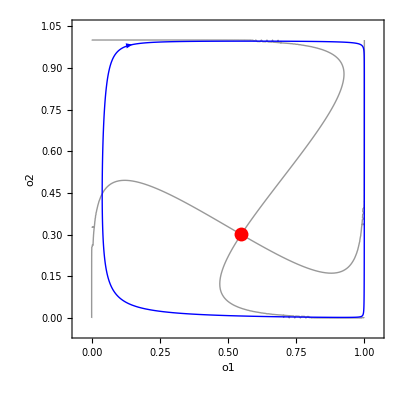

```mathematica
Show[
DisplayPhasePortrait[Ao2d/.{d->0.3},Tries->300,SaddleManifolds->True,SaddleManifoldDuration->10000,SaddleManifoldPlotPoints->1000,NullManifolds->True,AccuracyGoal->10,PlotRange->{{-.05,1.05},{-.05,1.05}},
LimitSets->{LC}]
]
```

#### Bifurcation Diagram with Limit-Cycle Branch

```mathematica
LCB=FollowLimitCycleBranch[LC,d,MaxStepSize->0.01];
```

```mathematica
Show[
DisplayBifurcationDiagram[Ao2d,d,Tries->300,LimitCycleBranches->{LCB},BifurcationPointStyle->{PointSize[0.012]},MaxStepSize->0.01,ViewPoint->{1.110396031150695,1.6853439215169146,1.0847287772576018},
AxesLabel->{"s","N_1","N_2"},AxesStyle->Directive[ Medium,Gray,FontFamily->"Ariel"]],
ImageSize->Medium
]
```

-Graphics3D-

```mathematica
BPs=$BifurcationDiagramBPs;
Length[BPs]
```

6

```mathematica
(* global bifurcations at BPs[[{4,5}]] *)
BPs[[5]]
```

BifurcationPoint[Fold,{0.87691784142836,0.00181208907182163},{d→0.393890184938678,sw1→15.98420800000000063789684645599,sw2→-4.954399999999999693045538151637,w11→9.382272000000000389263732358813,w12→-6.768112000000000350041773344856,w21→9.417232000000000269324118562508,w22→9.298944000000000542627276445273,w41→1.74254400000000009285372470913,w42→-13.63199999999999967315034155035,θ1→-14.31955199999999983617726684315,θ2→15.19025599999999975864284351701,τ1→29.98083099999999845408638066147,τ2→16.65731604999999859728632145561}]

LessEqual::nord: Invalid comparison with 1.+1.50871×10^-11 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

NDSolve::nbnum1: The function value !(9.×10^-6≤1.+1.50871×10^-11 ⅈ≤1.09999&&9.×10^-6≤0.838712-1.88497×10^-12 ⅈ≤1.09999) is not True or False when the arguments are {137.046,1.+1.50871×10^-11 ⅈ,0.838712-1.88497×10^-12 ⅈ}.

NDSolve::nbnum1: The function value !(9.×10^-6≤1.+5.40454×10^-11 ⅈ≤1.09999&&9.×10^-6≤0.838725-6.07177×10^-12 ⅈ≤1.09999) is not True or False when the arguments are {139.201,1.+5.40454×10^-11 ⅈ,0.838725-6.07177×10^-12 ⅈ}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 25000 steps reached at the point t == 156.685.

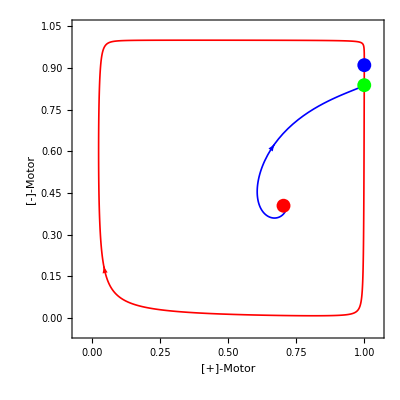

```mathematica
(* phase-portrait before global-bifurcation *)
DisplayPhasePortrait[Ao2d/.{d->0.19},Tries->300,SaddleManifolds->True,SaddleManifoldDuration->1000,SaddleManifoldPlotPoints->1000,NullManifolds->False,
PlotRange->{{-.05,1.05},{-.05,1.05}},FrameLabel->{"[+]-Motor","[-]-Motor"}]
```

```mathematica
DisplayBifurcationDiagram[Ao2d,d,LimitCycleBranches->{LCB},StateVariables->{o1},MaxStepSize->0.01,BifurcationPointStyle->{PointSize[0.01]}]
(* ,PlotRange->{{0,0.25},{-.05,1.05}} *)
```

-Graphics-

### Quasi-static Approximation

```mathematica
traj1=Import[FileNameJoin[{NotebookDirectory[],"naTraj1.txt"}],"Table"];
traj2=Import[FileNameJoin[{NotebookDirectory[],"naTraj2.txt"}],"Table"];
```

```mathematica
GraphicsGrid[{{
Show[
DisplayBifurcationDiagram[Ao2d,d,Tries->300,LimitCycleBranches->{LCB},StateVariables->{o1},MaxStepSize->0.01,BifurcationPointStyle->{PointSize[0.01]}],
ListLinePlot[{Drop[traj1,0,{3}]},PlotStyle->Brown]
],
Show[
DisplayBifurcationDiagram[Ao2d,d,Tries->300,LimitCycleBranches->{LCB},StateVariables->{o1},MaxStepSize->0.01,BifurcationPointStyle->{PointSize[0.01]}],
ListLinePlot[{Drop[traj2,0,{3}]},PlotStyle->Brown]
]
},{
Show[
DisplayBifurcationDiagram[Ao2d,d,Tries->300,LimitCycleBranches->{LCB},StateVariables->{o2},MaxStepSize->0.01,BifurcationPointStyle->{PointSize[0.01]}],
ListLinePlot[{Drop[traj1,0,{2}]},PlotStyle->Brown]
],
Show[
DisplayBifurcationDiagram[Ao2d,d,Tries->300,LimitCycleBranches->{LCB},StateVariables->{o2},MaxStepSize->0.01,BifurcationPointStyle->{PointSize[0.01]}],
ListLinePlot[{Drop[traj2,0,{2}]},PlotStyle->Brown]
]
}}]
```

-Graphics-

## (Pseudo-)Interaction Graph

Interaction Graph for Receiver in Phase 3

```mathematica
With[{c=Black},
GraphPlot[{Style[1->4,Red],Style[2->4,Blue],Style[2->5,Red],Style[3->5,Blue],Style[3->1,Red]},
DirectedEdges->True,EdgeStyle->Thick,
EdgeLabels->{
(2->4)->Style["P=1",Italic,FontSize->15,FontColor->c,FontFamily->"Cambria Math"],(2->5)->Style["P=2",Italic,FontSize->15,FontColor->c,FontFamily->"Cambria Math"]
},
VertexStyle->{1->Cyan,2->Cyan,3->Cyan,4->Red,5->Red},VertexSize->.08,
VertexCoordinates->{1->{1,2},2->{2,1.85},3->{3,2},4->{1,1},5->{3,1}},
VertexLabels->{
1->Placed[Style["Low",FontColor->c],Above],2->Placed[Style["Mid",FontColor->c],Above],3->Placed[Style["High",FontColor->c],Above],4->Placed[Style["Slow",FontColor->c],Below],5->Placed[Style["Fast",FontColor->c],Below]
}
]
]
```

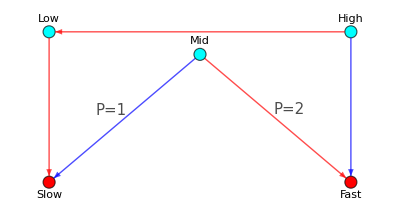

Complete Interaction Graph with Redundant Edges

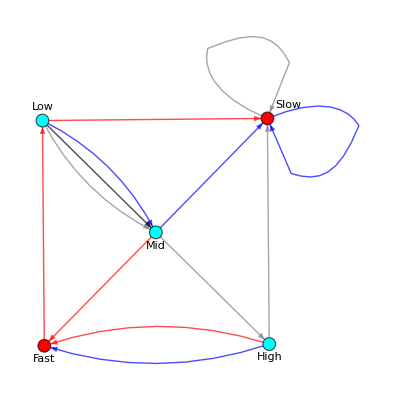

```mathematica
GraphPlot[
{Style[1->2,Blue],Style[1->4,Red],Style[1->2,Black],Style[1->2,Gray], Style[2->4,Blue],Style[2->3,Gray],Style[2->5,Red],Style[3->4,Gray],Style[3->5,Blue],Style[3->5,Red],Style[4->4,Gray],Style[4->4,Blue],Style[5->1,Red]},
DirectedEdges->True,EdgeStyle->Thick,
VertexStyle->{1->Cyan,2->Cyan,3->Cyan,4->Red,5->Red},VertexSize->.08,
VertexLabels->{
1->Placed[Style["Low",FontColor->Black,FontFamily->"Ariel"],Above],2->Placed[Style["Mid",FontColor->Black,FontFamily->"Ariel"],Below],3->Placed[Style["High",FontColor->Black,FontFamily->"Ariel"],Below],4->Placed[Style["Slow",FontColor->Black,FontFamily->"Ariel"],{After,Above}],5->Placed[Style["Fast",FontColor->Black,FontFamily->"Ariel"],Below]
}
]
```

Unravelling the graph for the receiver in Pu=1

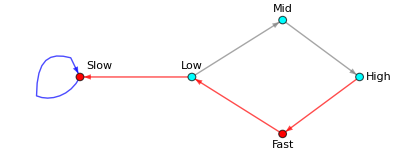

```mathematica
GraphPlot[
{Style[1->2,Gray],Style[2->3,Gray],Style[3->5,Red],Style[5->1,Red],Style[1->4,Red],Style[4->4,Blue]},
DirectedEdges->True,EdgeStyle->Thick,
VertexStyle->{1->Cyan,2->Cyan,3->Cyan,4->Red,5->Red},VertexSize->.08,
VertexLabels->{
1->Placed[Style["Low",FontColor->Black,FontFamily->"Ariel"],Above],2->Placed[Style["Mid",FontColor->Black,FontFamily->"Ariel"],Above],3->Placed[Style["High",FontColor->Black,FontFamily->"Ariel"],After],4->Placed[Style["Slow",FontColor->Black,FontFamily->"Ariel"],{After,Above}],5->Placed[Style["Fast",FontColor->Black,FontFamily->"Ariel"],Below]
}
]
```

Interaction Graph with Perturbation Classes

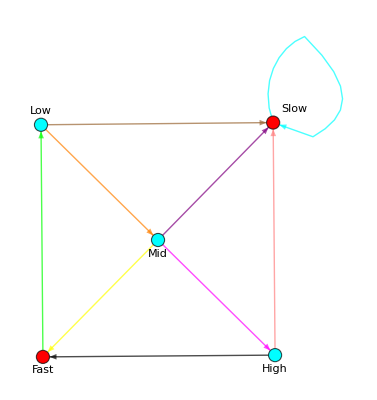

```mathematica
GraphPlot[
{Style[1->2,Orange],Style[1->4,Brown], Style[2->4,Purple],Style[2->3,Magenta],Style[2->5,Yellow],Style[3->4,Pink],Style[3->5,Black],Style[4->4,Cyan],Style[5->1,Green]},
DirectedEdges->True,EdgeStyle->Thick,
VertexStyle->{1->Cyan,2->Cyan,3->Cyan,4->Red,5->Red},VertexSize->.08,
VertexLabels->{
1->Placed[Style["Low",FontColor->Black,FontFamily->"Ariel"],Above],2->Placed[Style["Mid",FontColor->Black,FontFamily->"Ariel"],Below],3->Placed[Style["High",FontColor->Black,FontFamily->"Ariel"],Below],4->Placed[Style["Slow",FontColor->Black,FontFamily->"Ariel"],{After,Above}],5->Placed[Style["Fast",FontColor->Black,FontFamily->"Ariel"],Below]
}
]
```

## Additional Phase Portraits

### Agent 2 (Step-Type)

```mathematica
A2=SetPhenotype[2];
```

Import::nffil: File Pop-2/phenotype.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Part::take: Cannot take positions 1 through 5 in Flatten[$Failed].

Part::take: Cannot take positions 6 through 10 in Flatten[$Failed].

Part::take: Cannot take positions 11 through 35 in Flatten[$Failed].

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 3 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 4 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 5 of Flatten[$Failed]⟦1;;5⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(* Coordinates of first equilibrium point *)
equ2=EquilibriumPoints[A2/.{d->0}][[1,3]];
(* generating flow grid *)
flow2=Flatten[Table[Join[{equ2[[1]]},{i,j},equ2[[4;;]]],{i,-35,35,5},{j,-35,35,5}],1];
Length[flow2]
```

225

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 38.1328 and t = 38.5064.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 152.086 and t = 152.277.

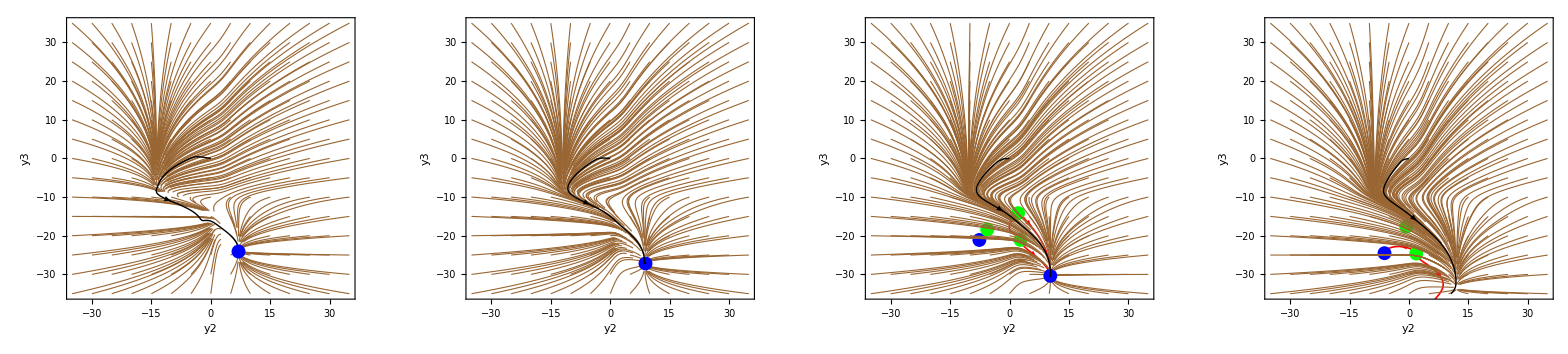

```mathematica
With[{i=0,j=.25,k=.5,l=.75},
GraphicsRow[{
Show[
DisplayPhasePortrait[A2/.{d->i},StateVariables->{y2,y3},SaddleManifolds->True],
DisplayTrajectories[A2/.{d->i},flow2,20,StateVariables->{y2,y3},Arrows->0],
DisplayTrajectories[A2/.{d->i},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y2,y3},PlotStyle->Black]
],
Show[
DisplayPhasePortrait[A2/.{d->j},StateVariables->{y2,y3},SaddleManifolds->True],
DisplayTrajectories[A2/.{d->j},flow2,20,StateVariables->{y2,y3},Arrows->0],
DisplayTrajectories[A2/.{d->j},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y2,y3},PlotStyle->Black]
],
Show[
DisplayPhasePortrait[A2/.{d->k},StateVariables->{y2,y3},SaddleManifolds->True],
DisplayTrajectories[A2/.{d->k},flow2,20,StateVariables->{y2,y3},Arrows->0],
DisplayTrajectories[A2/.{d->k},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y2,y3},PlotStyle->Black]
],
Show[
DisplayPhasePortrait[A2/.{d->l},StateVariables->{y2,y3},SaddleManifolds->True],
DisplayTrajectories[A2/.{d->l},flow2,20,StateVariables->{y2,y3},Arrows->0],
DisplayTrajectories[A2/.{d->l},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y2,y3},PlotStyle->Black]
]
}]
]
```

### Agent 3 (Basin-Type)

```mathematica
A3=SetPhenotype[3];
```

Import::nffil: File Pop-3/phenotype.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Part::take: Cannot take positions 1 through 5 in Flatten[$Failed].

Part::take: Cannot take positions 6 through 10 in Flatten[$Failed].

Part::take: Cannot take positions 11 through 35 in Flatten[$Failed].

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 3 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 4 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 5 of Flatten[$Failed]⟦1;;5⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A3/.{d->i},StateVariables->{y2,y4,y5},SaddleManifolds->True,SaddleManifoldDuration->1000,SaddleManifoldPlotPoints->1000,Tries->200],
DisplayTrajectories[A3/.{d->i},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y2,y4,y5}]
]
]
```

-Graphics3D-

### Agent 4 (Basin-Type)

```mathematica
A4=SetPhenotype[4];
```

Import::nffil: File Pop-4/phenotype.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Part::take: Cannot take positions 1 through 5 in Flatten[$Failed].

Part::take: Cannot take positions 6 through 10 in Flatten[$Failed].

Part::take: Cannot take positions 11 through 35 in Flatten[$Failed].

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 3 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 4 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 5 of Flatten[$Failed]⟦1;;5⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A4/.{d->i},StateVariables->{y1,y2,y5},SaddleManifolds->True,SaddleManifoldDuration->1000,SaddleManifoldPlotPoints->1000,Tries->200],
DisplayTrajectories[A4/.{d->i},{{0,0,0,0,0}},1000,PlotPoints->1000,StateVariables->{y1,y2,y5}]
]
]
```

-Graphics3D-

### Agent 5 (Step-Type)

```mathematica
A5=SetPhenotype[5];
```

Import::nffil: File Pop-5/phenotype.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Part::take: Cannot take positions 1 through 5 in Flatten[$Failed].

Part::take: Cannot take positions 6 through 10 in Flatten[$Failed].

Part::take: Cannot take positions 11 through 35 in Flatten[$Failed].

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 3 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 4 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 5 of Flatten[$Failed]⟦1;;5⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

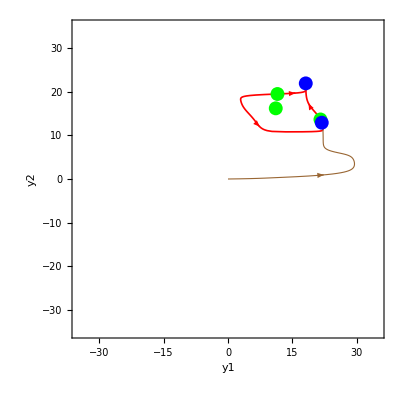

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A5/.{d->i},Tries->300,SaddleManifolds->True,SaddleManifoldPlotPoints->1000,SaddleManifoldDuration->1000,StateVariables->{y1,y2}],
DisplayTrajectories[A5/.{d->i},{{0,0,0,0,0}},500,PlotPoints->1000,StateVariables->{y1,y2}]
]
]
```

### Agent 6 (Step-Type)

```mathematica
A6=SetPhenotype[6];
```

Import::nffil: File Pop-6/phenotype.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Part::take: Cannot take positions 1 through 5 in Flatten[$Failed].

Part::take: Cannot take positions 6 through 10 in Flatten[$Failed].

Part::take: Cannot take positions 11 through 35 in Flatten[$Failed].

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 3 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 4 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 5 of Flatten[$Failed]⟦1;;5⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A6/.{d->i},Tries->300,SaddleManifolds->True,SaddleManifoldPlotPoints->1000,SaddleManifoldDuration->1000,StateVariables->{y1,y2,y5}],
DisplayTrajectories[A6/.{d->i},{{0,0,0,0,0}},500,PlotPoints->1000,StateVariables->{y1,y2,y5}]
]
]
```

-Graphics3D-

### Agent 7 (Basin-Type)

```mathematica
A7=SetPhenotype[7];
```

Import::nffil: File Pop-7/phenotype.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Part::take: Cannot take positions 1 through 5 in Flatten[$Failed].

Part::take: Cannot take positions 6 through 10 in Flatten[$Failed].

Part::take: Cannot take positions 11 through 35 in Flatten[$Failed].

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 3 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 4 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 5 of Flatten[$Failed]⟦1;;5⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A7/.{d->i},Tries->300,SaddleManifolds->True,SaddleManifoldPlotPoints->1000,SaddleManifoldDuration->1000,StateVariables->{y1,y2,y4}],
DisplayTrajectories[A7/.{d->i},{{0,0,0,0,0}},500,PlotPoints->1000,StateVariables->{y1,y2,y4}]
]
]
```

-Graphics3D-

### Agent 8 (Step-Type)

```mathematica
A8=SetPhenotype[8];
```

Import::nffil: File Pop-8/phenotype.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Part::take: Cannot take positions 1 through 5 in Flatten[$Failed].

Part::take: Cannot take positions 6 through 10 in Flatten[$Failed].

Part::take: Cannot take positions 11 through 35 in Flatten[$Failed].

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 3 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 4 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 5 of Flatten[$Failed]⟦1;;5⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A8/.{d->i},Tries->300,SaddleManifolds->True,SaddleManifoldPlotPoints->1000,SaddleManifoldDuration->1000,StateVariables->{y1,y2,y3}],
DisplayTrajectories[A8/.{d->i},{{0,0,0,0,0}},500,PlotPoints->1000,StateVariables->{y1,y2,y3}]
]
]
```

-Graphics3D-

### Agent 9 (Basin-Type)

```mathematica
A9=SetPhenotype[9];
```

Import::nffil: File Pop-9/phenotype.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Part::take: Cannot take positions 1 through 5 in Flatten[$Failed].

Part::take: Cannot take positions 6 through 10 in Flatten[$Failed].

Part::take: Cannot take positions 11 through 35 in Flatten[$Failed].

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 3 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 4 of Flatten[$Failed]⟦1;;5⟧ does not exist.

Part::partw: Part 5 of Flatten[$Failed]⟦1;;5⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
flow9=Tuples[{-35,35},5];
Length[flow9]
```

32

```mathematica
With[{i=0},
Show[
DisplayPhasePortrait[A9/.{d->i},Tries->500,SaddleManifolds->True,SaddleManifoldPlotPoints->1000,SaddleManifoldDuration->1000,StateVariables->{y1,y2,y5}],
DisplayTrajectories[A9/.{d->i},{{0,0,0,0,0}},500,PlotPoints->1000,StateVariables->{y1,y2,y5},PlotStyle->Black],
DisplayTrajectories[A9/.{d->i},flow9,500,PlotPoints->1000,StateVariables->{y1,y2,y5}]
]
]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 307.599 and t = 308.414.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 294.115 and t = 294.475.

-Graphics3D-